```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 595 Kb

{Utilities`CleanSlate`,GeneralRelativityTensors`,GeneralRelativityTensors`CommonTensors`,GeneralRelativityTensors`TensorDerivatives`,GeneralRelativityTensors`TensorManipulation`,GeneralRelativityTensors`TensorDefinitions`,GeneralRelativityTensors`Utils`,Notation`,VariationalMethods`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[R, 0]]
Symbolize[Subscript[Λ, 0]]
Symbolize[Subscript[ρ, 0]]
Symbolize[Subscript[p, 0]]
Symbolize[Subscript[Ω, Λ]]
Symbolize[Subscript[Ω, m]]
Symbolize[Subscript[Ω, k]]
Symbolize[Subscript[Ω, 𝓅]] (* use [esc]scp[esc] for 𝓅 NOT p otherwise won't be able to solve *)
Symbolize[Subscript[ρ, c]]
```

```mathematica
CreatePalette[{ 
PasteButton[Subscript[R, 0]],
PasteButton[Subscript[Λ, 0]],
PasteButton[Subscript[ρ, 0]],
PasteButton[Subscript[p, 0]] , 
PasteButton[Subscript[Ω, Λ]] , 
PasteButton[Subscript[Ω, m]] , 
PasteButton[Subscript[Ω, k]] ,
PasteButton[Subscript[Ω, 𝓅]] ,
PasteButton[Subscript[ρ, c]] 
}](* use [esc]scp[esc] for 𝓅 NOT p otherwise won't be able to solve *)
```

bpw74_shm32FrontEndObject[LinkObject["bpw74_shm", 3, 1]]32Untitled-5

```mathematica
Clear[eulerLagrangeEquations]
eulerLagrangeEquations[metric_, variables_ , parameter_ ]:= Module[
{q,qReplace,ℒ,eqs,eulerEquations} , 
Clear[q] ;
q = 
Flatten[Table[Map[variables[[i]],{parameter}] , {i,1,Length[variables]}]] ;
Clear[qReplace] ;
qReplace = 
Thread[
variables -> q ] ;
Clear[ℒ] ;
ℒ = 
Sum[(metric /. qReplace)[[i,j]] *   D[q,parameter][[i]] D[q,parameter][[j]] , {i,1, Length[q]},{j,1,Length[q]}] ;
Clear[eqs] ;
eqs = 
Table[
D[ D[ ℒ ,  D[q[[i]], parameter]] , parameter ] -D[ ℒ ,  q[[i]]]  , 
{i,1,Length[q]}] // Expand   ;
Clear[eulerEquations] ;
eulerEquations = 
Table[
Sum[
( Expand[eqs[[j]]][[i]] / Coefficient[eqs[[j]] ,D[D[q[[j]], parameter], parameter]]   ) , {i,1,Length[ Expand[eqs[[j]]]] } ] ,
{j,1,4}]  // Simplify 
];
```

```mathematica
Clear[input] 
input[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList];
tensorList = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList[[2]]  = 
ChristoffelSymbol[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[3]] = 
RiemannTensor[ tensorList[[1]] , ActWithNested-> Simplify ];
tensorList[[4]] = 
RicciTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[5]] = 
RicciScalar[ tensorList[[1]] , ActWith-> Simplify ] ;
 tensorList[[6]] = 
KretschmannScalar[ tensorList[[1]] , ActWith-> Simplify] ;  
 tensorList[[7]] = 
EinsteinTensor[ tensorList[[1]] , ActWith-> Simplify] ;    
tensorList[[8]] = 
WeylTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
 tensorList[[9]] = 
CottonTensor[ tensorList[[1]] , ActWith-> Simplify ] ; 
];
```

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[lineElement6pt1] (* Notice R-> R[t] for further metrics *) 
lineElement6pt1 = 
R^2(dx^2+dy^2+dz^2)/(( 1 + (1/4)k(x^2+y^2+z^2))^2)
```

((dx^2+dy^2+dz^2) R^2)/((1+1/4 k (x^2+y^2+z^2))^2)

```mathematica
Clear[metric6pt1]
metric6pt1 = 
lineToMetric[ lineElement6pt1 , { dx , dy , dz } ]  ;
metric6pt1 // MatrixForm
```

(R^2/((1+1/4 k (x^2+y^2+z^2))^2) | 0 | 0
0 | R^2/((1+1/4 k (x^2+y^2+z^2))^2) | 0
0 | 0 | R^2/((1+1/4 k (x^2+y^2+z^2))^2))

```mathematica
Clear[lineElement6pt3]
lineElement6pt3 = 
-dt^2+ R[t]^2(dx^2+dy^2+dz^2)/(( 1 + (1/4)k(x^2+y^2+z^2))^2)
```

-dt^2+((dx^2+dy^2+dz^2) R[t]^2)/((1+1/4 k (x^2+y^2+z^2))^2)

```mathematica
Clear[metric6pt3]
metric6pt3 = 
lineToMetric[ lineElement6pt3 , { dt , dx , dy , dz } ]  ;
metric6pt3 // MatrixForm
```

(-1 | 0 | 0 | 0
0 | R[t]^2/((1+1/4 k (x^2+y^2+z^2))^2) | 0 | 0
0 | 0 | R[t]^2/((1+1/4 k (x^2+y^2+z^2))^2) | 0
0 | 0 | 0 | R[t]^2/((1+1/4 k (x^2+y^2+z^2))^2))

```mathematica
Clear[inverse6pt3]
inverse6pt3 = 
Inverse[metric6pt3] ;
inverse6pt3 // MatrixForm
```

(-1 | 0 | 0 | 0
0 | ((1+1/4 k (x^2+y^2+z^2))^2)/R[t]^2 | 0 | 0
0 | 0 | ((1+1/4 k (x^2+y^2+z^2))^2)/R[t]^2 | 0
0 | 0 | 0 | ((1+1/4 k (x^2+y^2+z^2))^2)/R[t]^2)

```mathematica
eulerLagrangeEquations[ metric6pt3 , {t,x,y,z},u]  // Expand  // Simplify // TableForm
(* Not sure what's up *)
```

(16 R[t[u]] R'[t[u]] (x'[u]^2+y'[u]^2+z'[u]^2))/((4+k x[u]^2+k y[u]^2+k z[u]^2)^2)+t''[u]
(2 R'[t[u]] t'[u] x'[u])/R[t[u]]+(-4 k y[u] x'[u] y'[u]-4 k z[u] x'[u] z'[u]+2 k x[u] (-x'[u]^2+y'[u]^2+z'[u]^2)+4 x''[u]+k x[u]^2 x''[u]+k y[u]^2 x''[u]+k z[u]^2 x''[u])/(4+k x[u]^2+k y[u]^2+k z[u]^2)
(2 R'[t[u]] t'[u] y'[u])/R[t[u]]+(-4 k x[u] x'[u] y'[u]-4 k z[u] y'[u] z'[u]+2 k y[u] (x'[u]^2-y'[u]^2+z'[u]^2)+4 y''[u]+k x[u]^2 y''[u]+k y[u]^2 y''[u]+k z[u]^2 y''[u])/(4+k x[u]^2+k y[u]^2+k z[u]^2)
(2 R'[t[u]] t'[u] z'[u])/R[t[u]]+(-4 k x[u] x'[u] z'[u]-4 k y[u] y'[u] z'[u]+2 k z[u] (x'[u]^2+y'[u]^2-z'[u]^2)+4 z''[u]+k x[u]^2 z''[u]+k y[u]^2 z''[u]+k z[u]^2 z''[u])/(4+k x[u]^2+k y[u]^2+k z[u]^2)

```mathematica
input[ "metric6pt3", metric6pt3, "6pt3","g^dS6pt3",{t,x,y,z}, "Greek"] // Timing
```

{7.94462,Null}

```mathematica
TensorValues[tensorList[[1]]] // MatrixForm // pdConv
```

(-1 | 0 | 0 | 0
0 | (R(t))^2/((1/4 k (x^2+y^2+z^2)+1)^2) | 0 | 0
0 | 0 | (R(t))^2/((1/4 k (x^2+y^2+z^2)+1)^2) | 0
0 | 0 | 0 | (R(t))^2/((1/4 k (x^2+y^2+z^2)+1)^2))

```mathematica
TensorValues[tensorList[[2]]] // MatrixForm // pdConv
```

((0
0
0
0) | (0
(16 R(t) (∂R(t))/(∂t))/((k (x^2+y^2+z^2)+4)^2)
0
0) | (0
0
(16 R(t) (∂R(t))/(∂t))/((k (x^2+y^2+z^2)+4)^2)
0) | (0
0
0
(16 R(t) (∂R(t))/(∂t))/((k (x^2+y^2+z^2)+4)^2))
(0
((∂R(t))/(∂t))/(R(t))
0
0) | (((∂R(t))/(∂t))/(R(t))
-(2 k x)/(k (x^2+y^2+z^2)+4)
-(2 k y)/(k (x^2+y^2+z^2)+4)
-(2 k z)/(k (x^2+y^2+z^2)+4)) | (0
-(2 k y)/(k (x^2+y^2+z^2)+4)
(2 k x)/(k (x^2+y^2+z^2)+4)
0) | (0
-(2 k z)/(k (x^2+y^2+z^2)+4)
0
(2 k x)/(k (x^2+y^2+z^2)+4))
(0
0
((∂R(t))/(∂t))/(R(t))
0) | (0
(2 k y)/(k (x^2+y^2+z^2)+4)
-(2 k x)/(k (x^2+y^2+z^2)+4)
0) | (((∂R(t))/(∂t))/(R(t))
-(2 k x)/(k (x^2+y^2+z^2)+4)
-(2 k y)/(k (x^2+y^2+z^2)+4)
-(2 k z)/(k (x^2+y^2+z^2)+4)) | (0
0
-(2 k z)/(k (x^2+y^2+z^2)+4)
(2 k y)/(k (x^2+y^2+z^2)+4))
(0
0
0
((∂R(t))/(∂t))/(R(t))) | (0
(2 k z)/(k (x^2+y^2+z^2)+4)
0
-(2 k x)/(k (x^2+y^2+z^2)+4)) | (0
0
(2 k z)/(k (x^2+y^2+z^2)+4)
-(2 k y)/(k (x^2+y^2+z^2)+4)) | (((∂R(t))/(∂t))/(R(t))
-(2 k x)/(k (x^2+y^2+z^2)+4)
-(2 k y)/(k (x^2+y^2+z^2)+4)
-(2 k z)/(k (x^2+y^2+z^2)+4)))

```mathematica
TensorValues[tensorList[[3]]] // MatrixForm // pdConv
```

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -(16 R(t) (∂^2 R(t))/(∂t^2))/((k (x^2+y^2+z^2)+4)^2) | 0 | 0
(16 R(t) (∂^2 R(t))/(∂t^2))/((k (x^2+y^2+z^2)+4)^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -(16 R(t) (∂^2 R(t))/(∂t^2))/((k (x^2+y^2+z^2)+4)^2) | 0
0 | 0 | 0 | 0
(16 R(t) (∂^2 R(t))/(∂t^2))/((k (x^2+y^2+z^2)+4)^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -(16 R(t) (∂^2 R(t))/(∂t^2))/((k (x^2+y^2+z^2)+4)^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(16 R(t) (∂^2 R(t))/(∂t^2))/((k (x^2+y^2+z^2)+4)^2) | 0 | 0 | 0)
(0 | (16 R(t) (∂^2 R(t))/(∂t^2))/((k (x^2+y^2+z^2)+4)^2) | 0 | 0
-(16 R(t) (∂^2 R(t))/(∂t^2))/((k (x^2+y^2+z^2)+4)^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (256 (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k (x^2+y^2+z^2)+4)^4) | 0
0 | -(256 (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k (x^2+y^2+z^2)+4)^4) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (256 (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k (x^2+y^2+z^2)+4)^4)
0 | 0 | 0 | 0
0 | -(256 (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k (x^2+y^2+z^2)+4)^4) | 0 | 0)
(0 | 0 | (16 R(t) (∂^2 R(t))/(∂t^2))/((k (x^2+y^2+z^2)+4)^2) | 0
0 | 0 | 0 | 0
-(16 R(t) (∂^2 R(t))/(∂t^2))/((k (x^2+y^2+z^2)+4)^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -(256 (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k (x^2+y^2+z^2)+4)^4) | 0
0 | (256 (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k (x^2+y^2+z^2)+4)^4) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (256 (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k (x^2+y^2+z^2)+4)^4)
0 | 0 | -(256 (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k (x^2+y^2+z^2)+4)^4) | 0)
(0 | 0 | 0 | (16 R(t) (∂^2 R(t))/(∂t^2))/((k (x^2+y^2+z^2)+4)^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(16 R(t) (∂^2 R(t))/(∂t^2))/((k (x^2+y^2+z^2)+4)^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(256 (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k (x^2+y^2+z^2)+4)^4)
0 | 0 | 0 | 0
0 | (256 (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k (x^2+y^2+z^2)+4)^4) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(256 (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k (x^2+y^2+z^2)+4)^4)
0 | 0 | (256 (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k (x^2+y^2+z^2)+4)^4) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
TensorValues[tensorList[[4]]] // MatrixForm // pdConv
```

(-(3 (∂^2 R(t))/(∂t^2))/(R(t)) | 0 | 0 | 0
0 | (16 (2 k+R(t) (∂^2 R(t))/(∂t^2)+2 ((∂R(t))/(∂t))^2))/((k (x^2+y^2+z^2)+4)^2) | 0 | 0
0 | 0 | (16 (2 k+R(t) (∂^2 R(t))/(∂t^2)+2 ((∂R(t))/(∂t))^2))/((k (x^2+y^2+z^2)+4)^2) | 0
0 | 0 | 0 | (16 (2 k+R(t) (∂^2 R(t))/(∂t^2)+2 ((∂R(t))/(∂t))^2))/((k (x^2+y^2+z^2)+4)^2))

```mathematica
TensorValues[tensorList[[5]]] // MatrixForm // pdConv
```

(6 (k+R(t) (∂^2 R(t))/(∂t^2)+((∂R(t))/(∂t))^2))/(R(t))^2

```mathematica
TensorValues[tensorList[[6]]] // MatrixForm // pdConv
```

(12 (k^2+2 k ((∂R(t))/(∂t))^2+(R(t))^2 ((∂^2 R(t))/(∂t^2))^2+((∂R(t))/(∂t))^4))/(R(t))^4

```mathematica
TensorName[tensorList[[7]]]
TensorValues[tensorList[[7]]] // MatrixForm // pdConv
```

EinsteinTensor6pt3

((3 (k+((∂R(t))/(∂t))^2))/(R(t))^2 | 0 | 0 | 0
0 | -(16 (k+2 R(t) (∂^2 R(t))/(∂t^2)+((∂R(t))/(∂t))^2))/((k (x^2+y^2+z^2)+4)^2) | 0 | 0
0 | 0 | -(16 (k+2 R(t) (∂^2 R(t))/(∂t^2)+((∂R(t))/(∂t))^2))/((k (x^2+y^2+z^2)+4)^2) | 0
0 | 0 | 0 | -(16 (k+2 R(t) (∂^2 R(t))/(∂t^2)+((∂R(t))/(∂t))^2))/((k (x^2+y^2+z^2)+4)^2))

```mathematica
Clear[eq6pt12]
eq6pt12 = {
TensorValues[tensorList[[7]]] [[1,1]] , 
TensorValues[tensorList[[7]]] [[2,2]]
} ;
eq6pt12 // TableForm
```

(3 (k+R'[t]^2))/R[t]^2
-(16 (k+R'[t]^2+2 R[t] R''[t]))/((4+k (x^2+y^2+z^2))^2)

```mathematica
TensorValues[tensorList[[8]]] // MatrixForm // pdConv
```

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
TensorValues[tensorList[[9]]] // MatrixForm // pdConv
```

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0))

```mathematica
Clear[ℓ] 
ℓ = 
(1/(√2))*{ PowerExpand[Sqrt[-metric6pt3[[1,1]]]] ,PowerExpand[Sqrt[metric6pt3[[2,2]]]] ,0,0}
```

{1/(√2),R[t]/(√2 (1+1/4 k (x^2+y^2+z^2))),0,0}

```mathematica
Clear[𝓃]
𝓃 =
(1/(√2))*{ PowerExpand[Sqrt[-metric6pt3[[1,1]]]] , -PowerExpand[Sqrt[metric6pt3[[2,2]]]] ,0,0}
```

{1/(√2),-R[t]/(√2 (1+1/4 k (x^2+y^2+z^2))),0,0}

```mathematica
Clear[𝓂]
𝓂 =
(1/(√2))*{0,0, PowerExpand[Sqrt[metric6pt3[[3,3]]]] , ⅈ PowerExpand[Sqrt[metric6pt3[[4,4]]]] }
```

{0,0,R[t]/(√2 (1+1/4 k (x^2+y^2+z^2))),(ⅈ R[t])/(√2 (1+1/4 k (x^2+y^2+z^2)))}

```mathematica
Clear[𝓂bar]
𝓂bar =
(1/(√2))*{0,0, PowerExpand[Sqrt[metric6pt3[[3,3]]]] , -ⅈ PowerExpand[Sqrt[metric6pt3[[4,4]]]] }
```

{0,0,R[t]/(√2 (1+1/4 k (x^2+y^2+z^2))),-(ⅈ R[t])/(√2 (1+1/4 k (x^2+y^2+z^2)))}

```mathematica
(* ALWAYS ALWAYS ALWAYS CHECK IF INDICES ARE UP OR DOWN !!!!! *)
l = ToTensor[ {"NewTensor" , "l"} , tensorList[[1]] , ℓ , {-μ}]
n = ToTensor[{"NewTensor" , "n" } , tensorList[[1]] , 𝓃 , {-μ} ] 
m = ToTensor[{"NewTensor" , "m" } , tensorList[[1]] , 𝓂 , {-μ} ] 
mbar = ToTensor[{"NewTensor" , "mbar" } , tensorList[[1]] , 𝓂bar , {-μ} ]
```

l_μ^

n_μ^

m_μ^

mbar_μ^

```mathematica
TensorValues[ContractIndices[l[-μ]l[μ]]] == 0  // Expand // Simplify 
TensorValues[ContractIndices[n[-μ]n[μ]] ]== 0  // Expand // Simplify 
TensorValues[ContractIndices[m[-μ]m[μ]]] == 0   // Expand // FullSimplify 
TensorValues[ContractIndices[mbar[-μ]mbar[μ]]] == 0  // Expand // FullSimplify 
TensorValues[ContractIndices[l[-μ]n[μ]]] == -1// Expand // FullSimplify 
TensorValues[ContractIndices[l[μ]n[-μ]]] == -1  // Expand // FullSimplify 
TensorValues[ContractIndices[m[-μ]mbar[μ]]] ==  1 // Expand // FullSimplify 
TensorValues[ContractIndices[m[μ]mbar[-μ]]] ==  1 // Expand // FullSimplify 
Clear[completenessDownIndices]
completenessDownIndices = 
MergeTensors[-l[-μ]n[-ν]-n[-μ]l[-ν] + m[-μ]mbar[-ν]+m[-ν]mbar[-μ]]  ;
TensorValues[ completenessDownIndices ]  // MatrixForm

Thread[Flatten[metric6pt3] == 
Flatten[ TensorValues[ completenessDownIndices ]] ] // Expand // FullSimplify 

Clear[completenessUpIndices]
completenessUpIndices = 
MergeTensors[-l[μ]n[ν]-n[μ]l[ν] + m[μ]mbar[ν]+ m[ν]mbar[μ]]  ;
TensorValues[ completenessUpIndices ]  // MatrixForm

Thread[Flatten[inverse6pt3] == 
Flatten[ TensorValues[ completenessUpIndices ]] ]  // Expand // FullSimplify
```

True

True

True

«5 more identical outputs»

(-1 | 0 | 0 | 0
0 | R[t]^2/((1+1/4 k (x^2+y^2+z^2))^2) | 0 | 0
0 | 0 | R[t]^2/((1+1/4 k (x^2+y^2+z^2))^2) | 0
0 | 0 | 0 | R[t]^2/((1+1/4 k (x^2+y^2+z^2))^2))

True

(-1 | 0 | 0 | 0
0 | ((1+1/4 k (x^2+y^2+z^2))^2)/R[t]^2 | 0 | 0
0 | 0 | ((1+1/4 k (x^2+y^2+z^2))^2)/R[t]^2 | 0
0 | 0 | 0 | ((1+1/4 k (x^2+y^2+z^2))^2)/R[t]^2)

True

```mathematica
Clear[spinCoefficientReplace]  (* Page 56 Wang *) (* check where these definitions came from *)
spinCoefficientReplace= {
ρ ->(  MergeTensors[ CovariantD[ l[-μ],-ν] m[μ] mbar[ν] ] // TensorValues  // Expand // FullSimplify )  , 
μ-> (*note minus sign *)(-1)*( MergeTensors [ CovariantD[ n[-μ] , -ν ] mbar[μ] m[ν] ] // TensorValues  // Expand  // FullSimplify )  , 
ε -> ( (1/2)(( MergeTensors[CovariantD[l[-μ],-ν] n[μ] l[ν]] // TensorValues  // Expand  // FullSimplify  )  - 
(MergeTensors[ CovariantD[ m[-μ],-ν] mbar[μ] l[ν]] // TensorValues // Expand // FullSimplify) ) // Expand  // FullSimplify ) , 
γ -> (* something weird here correct definition off by minus sign *) ((1/2)((MergeTensors[CovariantD[ l[-μ],-ν] n[μ]n[ν] ] // TensorValues  // Expand  )-
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] n[ν]] // TensorValues // Expand  // FullSimplify )) // Expand ) , 
σ->( MergeTensors[ CovariantD[l[-μ] , -ν] m[μ] m[ν]] // TensorValues  // Expand // FullSimplify)  , 
λ-> (* note minus sign *)(-1)*( MergeTensors[ CovariantD[ n[-μ],-ν] mbar[μ] mbar[ν] ]  // TensorValues // Expand // FullSimplify)  ,
κ->(  MergeTensors[ CovariantD[ l[-μ] ,-ν] m[μ] l[ν]  ]  // TensorValues ) , 
ν-> ( MergeTensors[ CovariantD[ n[-μ],-ν]m[μ] n[ν] ] // TensorValues ) , 
τ->( MergeTensors[ CovariantD[ l[-μ],-ν] m[μ] n[ν ]]// TensorValues ) , 
π-> (* Note minus sign *)(-1)* (MergeTensors[CovariantD[ n[-μ],-ν] mbar[μ] l[ν]] // TensorValues  // Expand ) , 
α-> ((1/2)((MergeTensors[CovariantD[ l[-μ],-ν] n[μ] mbar[ν]] // TensorValues )-
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] mbar[ν]] // TensorValues)) ) , 
β -> (* Spin coefficient β *) 
((1/2)((MergeTensors[ CovariantD[ l[-μ],-ν] n[μ]m[ν]] // TensorValues)- 
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] m[ν]] // TensorValues )))
} ;
spinCoefficientReplace // TableForm // pdConv
```

ρ→-(k x+2 (∂R(t))/(∂t))/(2 √2 R(t))
μ→-(k x-2 (∂R(t))/(∂t))/(2 √2 R(t))
ε→((∂R(t))/(∂t))/(2 √2 R(t))
γ→-((∂R(t))/(∂t))/(2 √2 R(t))
σ→0
λ→0
κ→(k y)/(4 √2 R(t))+(ⅈ k z)/(4 √2 R(t))
ν→(k y)/(4 √2 R(t))+(ⅈ k z)/(4 √2 R(t))
τ→-(k y)/(4 √2 R(t))-(ⅈ k z)/(4 √2 R(t))
π→(k y)/(4 √2 R(t))-(ⅈ k z)/(4 √2 R(t))
α→1/2 (-(k y)/(2 √2 R(t))+(ⅈ k z)/(2 √2 R(t)))
β→1/2 ((k y)/(2 √2 R(t))+(ⅈ k z)/(2 √2 R(t)))

```mathematica
(* I don't think this is right *)
```

```mathematica
Clear[ricciScalarsReplace] (* Definitions from Griffiths *) 
(* Page 57 Wang *) 
ricciScalarsReplace = {
Subscript[Φ, oo]-> (* be careful about oh's not zeros *) 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]l[μ]l[ν]]] // Expand // FullSimplify  , 
Subscript[Φ, O1]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]l[μ]m[ν]]] // Expand // FullSimplify, 
Subscript[Φ, O2]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]m[μ]m[ν]]] // Expand // FullSimplify, 
Subscript[Φ, 11]-> 
(-1/4)*( ( TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]l[μ]n[ν]]])+ (TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]m[μ]mbar[ν]]])) // Expand // FullSimplify, 
Subscript[Φ, 12]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]n[μ]m[ν]]] // Expand // FullSimplify, 
Subscript[Φ, 22]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]n[μ]n[ν]]]// Expand // FullSimplify , 
Λ-> 
(1/24)*TensorValues[tensorList[[5]]]// Expand // FullSimplify
} ;
ricciScalarsReplace  // TableForm // pdConv
```

Φ_oo→-(k-R(t) (∂^2 R(t))/(∂t^2)+((∂R(t))/(∂t))^2)/(2 (R(t))^2)
Φ_O1→0
Φ_O2→0
Φ_11→-(k-R(t) (∂^2 R(t))/(∂t^2)+((∂R(t))/(∂t))^2)/(4 (R(t))^2)
Φ_12→0
Φ_22→-(k-R(t) (∂^2 R(t))/(∂t^2)+((∂R(t))/(∂t))^2)/(2 (R(t))^2)
Λ→(k+R(t) (∂^2 R(t))/(∂t^2)+((∂R(t))/(∂t))^2)/(4 (R(t))^2)

```mathematica
(* I don't think this is right *)
```

```mathematica
Clear[weylScalarsReplace](* Definitions from Griffiths *) 
(* Page 57 Wang *) 
weylScalarsReplace = {

Subscript[Ψ, 0]-> (-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]l[κ]m[λ]l[μ]m[ν]]]// Expand // FullSimplify , 
Subscript[Ψ, 1]-> (-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]l[κ]n[λ]l[μ]m[ν]]]// Expand // FullSimplify , 
Subscript[Ψ, 2]-> (-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]l[κ]m[λ]mbar[μ]n[ν]]] // Expand // FullSimplify, 
Subscript[Ψ, 3]-> (-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]n[κ]l[λ]n[μ]mbar[ν]]]// Expand // FullSimplify , 
Subscript[Ψ, 4]-> (-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]n[κ]mbar[λ]n[μ]mbar[ν]]]// Expand // FullSimplify
} ;
weylScalarsReplace // TableForm // pdConv
```

Ψ_0→0
Ψ_1→0
Ψ_2→0
Ψ_3→0
Ψ_4→0

```mathematica
Clear[lineElement6pt4]
lineElement6pt4= 
-dt^2+ R[t]^2 (dθ^2 r^2+dr^2/(1-k r^2)+dϕ^2 r^2 Sin[θ]^2)
```

-dt^2+R[t]^2 (dθ^2 r^2+dr^2/(1-k r^2)+dϕ^2 r^2 Sin[θ]^2)

```mathematica
Clear[metric6pt4]
metric6pt4 = 
lineToMetric[ lineElement6pt4 , { dt , dr , dθ , dϕ } ] ;
metric6pt4 // MatrixForm
```

(-1 | 0 | 0 | 0
0 | R[t]^2/(1-k r^2) | 0 | 0
0 | 0 | r^2 R[t]^2 | 0
0 | 0 | 0 | r^2 R[t]^2 Sin[θ]^2)

```mathematica
eulerLagrangeEquations[ metric6pt4 , {t,r,θ,ϕ} , u ]  // TableForm
```

R[t[u]] R'[t[u]] (r'[u]^2/(1-k r[u]^2)+r[u]^2 (θ'[u]^2+Sin[θ[u]]^2 ϕ'[u]^2))+t''[u]
(k r[u] r'[u]^2)/(1-k r[u]^2)+(2 r'[u] R'[t[u]] t'[u])/R[t[u]]+r[u] (-1+k r[u]^2) θ'[u]^2+r[u] (-1+k r[u]^2) Sin[θ[u]]^2 ϕ'[u]^2+r''[u]
(2 r'[u] θ'[u])/r[u]+(2 R'[t[u]] t'[u] θ'[u])/R[t[u]]-Cos[θ[u]] Sin[θ[u]] ϕ'[u]^2+θ''[u]
(2 r'[u] ϕ'[u])/r[u]+(2 R'[t[u]] t'[u] ϕ'[u])/R[t[u]]+2 Cot[θ[u]] θ'[u] ϕ'[u]+ϕ''[u]

```mathematica
Clear[lineElement6pt5] (* k = 0 *) 
lineElement6pt5 = 
-dt^2+R[t]^2 (dχ^2+dθ^2 χ^2+dϕ^2 χ^2 Sin[θ]^2)
```

-dt^2+R[t]^2 (dχ^2+dθ^2 χ^2+dϕ^2 χ^2 Sin[θ]^2)

```mathematica
Clear[ metric6pt5 ] 
metric6pt5  =  
lineToMetric[ lineElement6pt5 , { dt , dχ , dθ , dϕ } ]  ;
metric6pt5  // MatrixForm
```

(-1 | 0 | 0 | 0
0 | R[t]^2 | 0 | 0
0 | 0 | χ^2 R[t]^2 | 0
0 | 0 | 0 | χ^2 R[t]^2 Sin[θ]^2)

```mathematica
eulerLagrangeEquations[ metric6pt5 , {t,χ,θ,ϕ} ,u ]  // TableForm
```

R[t[u]] R'[t[u]] (χ[u]^2 (θ'[u]^2+Sin[θ[u]]^2 ϕ'[u]^2)+χ'[u]^2)+t''[u]
-χ[u] (θ'[u]^2+Sin[θ[u]]^2 ϕ'[u]^2)+(2 R'[t[u]] t'[u] χ'[u])/R[t[u]]+χ''[u]
(2 R'[t[u]] t'[u] θ'[u])/R[t[u]]-Cos[θ[u]] Sin[θ[u]] ϕ'[u]^2+(2 θ'[u] χ'[u])/χ[u]+θ''[u]
(2 R'[t[u]] t'[u] ϕ'[u])/R[t[u]]+2 Cot[θ[u]] θ'[u] ϕ'[u]+(2 ϕ'[u] χ'[u])/χ[u]+ϕ''[u]

```mathematica
Clear[lineElement6pt6] (* k = +1 *) 
lineElement6pt6 = 
-dt^2+ R[t]^2 (dχ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sin[χ]^2)
```

-dt^2+R[t]^2 (dχ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sin[χ]^2)

```mathematica
Clear[metric6pt6]
metric6pt6  = 
lineToMetric[ lineElement6pt6 ,  { dt , dχ , dθ , dϕ } ] ;
metric6pt6 // MatrixForm
```

(-1 | 0 | 0 | 0
0 | R[t]^2 | 0 | 0
0 | 0 | R[t]^2 Sin[χ]^2 | 0
0 | 0 | 0 | R[t]^2 Sin[θ]^2 Sin[χ]^2)

```mathematica
eulerLagrangeEquations[ metric6pt6 , {t,χ,θ,ϕ} , u ]  // TableForm
```

R[t[u]] R'[t[u]] (Sin[χ[u]]^2 θ'[u]^2+Sin[θ[u]]^2 Sin[χ[u]]^2 ϕ'[u]^2+χ'[u]^2)+t''[u]
-Cos[χ[u]] Sin[χ[u]] θ'[u]^2-Cos[χ[u]] Sin[θ[u]]^2 Sin[χ[u]] ϕ'[u]^2+(2 R'[t[u]] t'[u] χ'[u])/R[t[u]]+χ''[u]
(2 R'[t[u]] t'[u] θ'[u])/R[t[u]]-Cos[θ[u]] Sin[θ[u]] ϕ'[u]^2+2 Cot[χ[u]] θ'[u] χ'[u]+θ''[u]
(2 R'[t[u]] t'[u] ϕ'[u])/R[t[u]]+2 Cot[θ[u]] θ'[u] ϕ'[u]+2 Cot[χ[u]] ϕ'[u] χ'[u]+ϕ''[u]

```mathematica
Clear[lineElement6pt7] (* k = - 1 *) 
lineElement6pt7 = 
-dt^2+R[t]^2 (dχ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sinh[χ]^2)
```

-dt^2+R[t]^2 (dχ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sinh[χ]^2)

```mathematica
Clear[metric6pt7]
metric6pt7 = 
lineToMetric[ lineElement6pt7 , { dt , dχ , dθ , dϕ } ]  ;
metric6pt7 // MatrixForm
```

(-1 | 0 | 0 | 0
0 | R[t]^2 | 0 | 0
0 | 0 | R[t]^2 Sinh[χ]^2 | 0
0 | 0 | 0 | R[t]^2 Sin[θ]^2 Sinh[χ]^2)

```mathematica
eulerLagrangeEquations[ metric6pt7 , {t,χ,θ,ϕ} , u ]  // TableForm
```

R[t[u]] R'[t[u]] (Sinh[χ[u]]^2 θ'[u]^2+Sin[θ[u]]^2 Sinh[χ[u]]^2 ϕ'[u]^2+χ'[u]^2)+t''[u]
-Cosh[χ[u]] Sinh[χ[u]] θ'[u]^2-Cosh[χ[u]] Sin[θ[u]]^2 Sinh[χ[u]] ϕ'[u]^2+(2 R'[t[u]] t'[u] χ'[u])/R[t[u]]+χ''[u]
(2 R'[t[u]] t'[u] θ'[u])/R[t[u]]-Cos[θ[u]] Sin[θ[u]] ϕ'[u]^2+2 Coth[χ[u]] θ'[u] χ'[u]+θ''[u]
(2 R'[t[u]] t'[u] ϕ'[u])/R[t[u]]+2 Cot[θ[u]] θ'[u] ϕ'[u]+2 Coth[χ[u]] ϕ'[u] χ'[u]+ϕ''[u]

```mathematica
Clear[eq6pt10]
eq6pt10 = 
p[t] == (γ-1) ρ[t]
```

p[t]==(-1+γ) ρ[t]

```mathematica
Clear[eq6pt11]
eq6pt11 = 
ρ[t] == 𝒞/R[t]^(3 γ)
```

ρ[t]==𝒞 R[t]^(-3 γ)

```mathematica
eq6pt11 /. γ-> 1 (* dust *) 
eq6pt11 /. γ-> 4/3  (* radiation *)
eq6pt11 /. γ-> 2 (* stiff *) 
eq6pt11 /. γ-> 0 (* cosmological constant *)
```

ρ[t]==𝒞/R[t]^3

ρ[t]==𝒞/R[t]^4

ρ[t]==𝒞/R[t]^6

ρ[t]==𝒞

```mathematica
Clear[eq6pt15]
eq6pt15 = 
R'[t]^2/R[t]^2== Λ/3- k/R[t]^2+ c/R[t]^(3 γ) (* /.  c-> ((8 π)/3) 𝒞  *) (* uncomment if needed be sure to use [esc]scC[esc] for 𝒞 as C is protected *)
```

R'[t]^2/R[t]^2==Λ/3-k/R[t]^2+c R[t]^(-3 γ)

```mathematica
Clear[eq6pt16]
eq6pt16 = (* use R for plots, then back substitute R->R[t] *) 
V[R] ->  ( k/R^2- (1/R^(3 γ))((3 c)/(8 π))) (* /. c-> ((8 π)/3)𝒞 *)
```

V[R]→k/R^2-(3 c R^(-3 γ))/(8 π)

```mathematica
eq6pt16 /. c-> 0  /. k-> 1   (* cosmological constant or vacuum?  REDO *) 
eq6pt16 /. c-> 1  /. k-> 1  /. γ-> 1 (* dust *) 
eq6pt16 /. c-> 1  /. k-> 1  /. γ-> 4/3 (* raditiation *) 
eq6pt16 /. c-> 1  /. k-> 1  /. γ-> 2 (* stiff *)
```

V[R]→1/R^2

V[R]→-3/(8 π R^3)+1/R^2

V[R]→-3/(8 π R^4)+1/R^2

V[R]→-3/(8 π R^6)+1/R^2

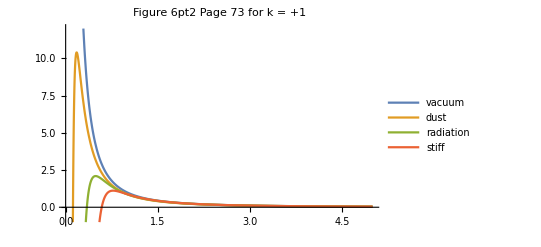

```mathematica
Plot[
Evaluate[
{
V[R] /. ( eq6pt16 /. c-> 0  /. k-> 1  ) ,(* cosmological constant *) 
V[R] /.(  eq6pt16 /. c-> 1  /. k-> 1  /. γ-> 1 ) , (* dust *) 
V[R] /. ( eq6pt16 /. c-> 1  /. k-> 1  /. γ-> 4/3  ) ,(* raditiation *)
V[R] /.  ( eq6pt16 /. c-> 1  /. k-> 1  /. γ-> 2  ) (* stiff *) 
}
] , { R , 0 , 5 } , 
PlotLegends-> {"vacuum" , "dust" , "radiation" , "stiff" } , PlotRange-> { -1 , 12 } ,
PlotLabel-> "Figure 6pt2 Page 73 for k = +1" ]
```

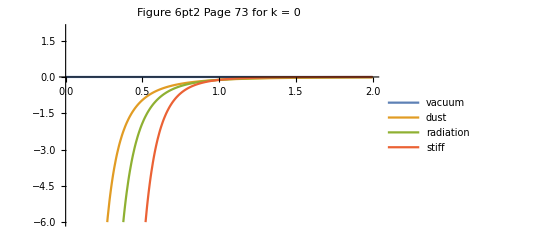

```mathematica
Plot[
Evaluate[
{
V[R] /. ( eq6pt16 /. c-> 0  /. k-> 0  ) ,(* cosmological constant *) 
V[R] /.(  eq6pt16 /. c-> 1  /. k-> 0  /. γ-> 1 ) , (* dust *) 
V[R] /. ( eq6pt16 /. c-> 1  /. k-> 0  /. γ-> 4/3  ) ,(* raditiation *)
V[R] /.  ( eq6pt16 /. c-> 1  /. k-> 0  /. γ-> 2  ) (* stiff *) 
}
] , { R , 0 , 2 } , 
PlotLegends-> {"vacuum" , "dust" , "radiation" , "stiff" } , PlotRange-> { -6 , 2 } ,
PlotLabel-> "Figure 6pt2 Page 73 for k = 0" ]
```

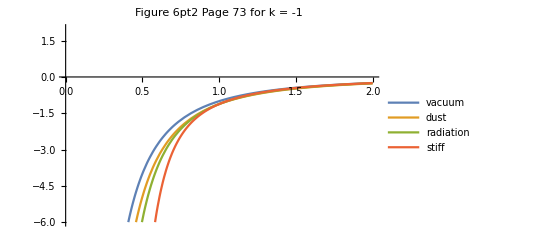

```mathematica
Plot[
Evaluate[
{
V[R] /. ( eq6pt16 /. c-> 0  /. k-> -1  ) ,(* cosmological constant *) 
V[R] /.(  eq6pt16 /. c-> 1  /. k-> -1  /. γ-> 1 ) , (* dust *) 
V[R] /. ( eq6pt16 /. c-> 1  /. k-> -1  /. γ-> 4/3  ) ,(* raditiation *)
V[R] /.  ( eq6pt16 /. c-> 1  /. k-> -1  /. γ-> 2  ) (* stiff *) 
}
] , { R , 0 , 2 } , 
PlotLegends-> {"vacuum" , "dust" , "radiation" , "stiff" } , PlotRange-> { -6 , 2 } ,
PlotLabel-> "Figure 6pt2 Page 73 for k = -1" ]
```

```mathematica
Clear[lineElement6pt19]
lineElement6pt19 = 
- dt^2 + t^2( dχ^2+Sinh[χ]^2 ( dθ^2 + Sin[θ]^2  dϕ^2 ) )
```

-dt^2+t^2 (dχ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sinh[χ]^2)

```mathematica
(* REDO DSolve using proper assumptions to get three different solutions *)
```

```mathematica
Clear[metric6pt19]
metric6pt19 = 
lineToMetric[ Collect[ Expand[lineElement6pt19] , { dt , dχ , dθ , dϕ } ] , { dt , dχ , dθ , dϕ } ]  ;
metric6pt19 // MatrixForm
```

(-1 | 0 | 0 | 0
0 | t^2 | 0 | 0
0 | 0 | t^2 Sinh[χ]^2 | 0
0 | 0 | 0 | t^2 Sin[θ]^2 Sinh[χ]^2)

```mathematica
eulerLagrangeEquations[ metric6pt19 , {t,χ,θ,ϕ} , u ]  // TableForm
```

t[u] (Sinh[χ[u]]^2 θ'[u]^2+Sin[θ[u]]^2 Sinh[χ[u]]^2 ϕ'[u]^2+χ'[u]^2)+t''[u]
-Cosh[χ[u]] Sinh[χ[u]] θ'[u]^2-Cosh[χ[u]] Sin[θ[u]]^2 Sinh[χ[u]] ϕ'[u]^2+(2 t'[u] χ'[u])/t[u]+χ''[u]
(2 t'[u] θ'[u])/t[u]-Cos[θ[u]] Sin[θ[u]] ϕ'[u]^2+2 Coth[χ[u]] θ'[u] χ'[u]+θ''[u]
(2 t'[u] ϕ'[u])/t[u]+2 Cot[θ[u]] θ'[u] ϕ'[u]+2 Coth[χ[u]] ϕ'[u] χ'[u]+ϕ''[u]

```mathematica
( eq6pt15 /. c-> 0  /. k-> 1 /. Λ-> 3/a^2  )
```

R'[t]^2/R[t]^2==1/a^2-1/R[t]^2

```mathematica
Assuming[ a > 0 , 
DSolve[ ( eq6pt15 /. c-> 0  /. k-> 1 /. Λ-> 3/a^2  ) , R[t] , t ]][[1]]  /. C[1]-> 0  // Expand  // TrigReduce
```

{R[t]→-1/2 ⅈ a ⅇ^(-t/a)+1/2 ⅈ a ⅇ^(t/a)}

```mathematica
Clear[eq6pt19b]
eq6pt19b = {
R[t]-> a Cosh[t/a] , 
R[t]-> a Exp[t/a] , 
R[t]-> a Sinh[t/a]
} ;
eq6pt19b // TableForm
```

R[t]→a Cosh[t/a]
R[t]→a ⅇ^(t/a)
R[t]→a Sinh[t/a]

```mathematica
eq6pt19b[[1]]
D[eq6pt19b[[1]], t]
```

R[t]→a Cosh[t/a]

R'[t]→Sinh[t/a]

```mathematica
( eq6pt15 /. c-> 0  /. k-> 1   /.  Λ-> 3/a^2) /. eq6pt19b[[1]] /. D[eq6pt19b[[1]], t] // Expand // Simplify 
( eq6pt15 /. c-> 0  /. k-> 0   /.  Λ-> 3/a^2) /. eq6pt19b[[2]] /. D[eq6pt19b[[2]], t] // Expand // Simplify 
( eq6pt15 /. c-> 0  /. k-> -1   /.  Λ-> 3/a^2) /. eq6pt19b[[3]] /. D[eq6pt19b[[3]], t] // Expand // Simplify
```

True

True

True

```mathematica
(* Page 76 6.3.2 *) 
Clear[eq6pt3pt2]
eq6pt3pt = 
Assuming[ R[t]^2 ≠ 0 , 
MultiplySides[ ( eq6pt15 /. Λ-> 0   ) , R[t]^2 ] ]  // Expand
```

R'[t]^2==-k+c R[t]^(2-3 γ)

```mathematica
eq6pt3pt /. k -> 1  
eq6pt3pt /. k -> 0  
eq6pt3pt /. k -> -1
```

R'[t]^2==-1+c R[t]^(2-3 γ)

R'[t]^2==c R[t]^(2-3 γ)

R'[t]^2==1+c R[t]^(2-3 γ)

```mathematica
DSolve[ ( eq6pt3pt /. k -> 1   ) , R[t] , t ] 
DSolve[ ( eq6pt3pt /. k -> 0   ) , R[t] , t ]  /. C[1]-> 0  (* This looks o.k., redo other two *) 
DSolve[ ( eq6pt3pt /. k -> -1   ) , R[t] , t ]
```

{{R[t]→InverseFunction[(Hypergeometric2F1[1/2,1/(2-3 γ),1+1/(2-3 γ),c #1^(2-3 γ)] #1 √(1-c #1^(2-3 γ)))/(√(-1+c #1^(2-3 γ)))&][-t+C[1]]},{R[t]→InverseFunction[(Hypergeometric2F1[1/2,1/(2-3 γ),1+1/(2-3 γ),c #1^(2-3 γ)] #1 √(1-c #1^(2-3 γ)))/(√(-1+c #1^(2-3 γ)))&][t+C[1]]}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{R[t]→(3/2)^(2/3/γ) (√c t γ)^(2/3/γ)},{R[t]→(3/2)^(2/3/γ) (-√c t γ)^(2/3/γ)}}

{{R[t]→InverseFunction[Hypergeometric2F1[1/2,1/(2-3 γ),1+1/(2-3 γ),-c #1^(2-3 γ)] #1&][-t+C[1]]},{R[t]→InverseFunction[Hypergeometric2F1[1/2,1/(2-3 γ),1+1/(2-3 γ),-c #1^(2-3 γ)] #1&][t+C[1]]}}

```mathematica
(* REDO to get plots on page 77 *)
```

```mathematica
lineElement6pt6

Clear[lineElement6pt21a]
lineElement6pt21a = 
Collect[ lineElement6pt6 /.  dt-> R[η] dη  /. R[t]-> R[η] // Expand , R[η]]
```

-dt^2+R[t]^2 (dχ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sin[χ]^2)

R[η]^2 (-dη^2+dχ^2+dθ^2 Sin[χ]^2+dϕ^2 Sin[θ]^2 Sin[χ]^2)

```mathematica
Clear[metric6pt21a] (* for k = +1 *) 
metric6pt21a = 
lineToMetric[ lineElement6pt21a , { dη , dχ , dθ , dϕ } ] ;
metric6pt21a // MatrixForm
```

(-R[η]^2 | 0 | 0 | 0
0 | R[η]^2 | 0 | 0
0 | 0 | R[η]^2 Sin[χ]^2 | 0
0 | 0 | 0 | R[η]^2 Sin[θ]^2 Sin[χ]^2)

```mathematica
eulerLagrangeEquations[ metric6pt21a , {η,χ,θ,ϕ} , u ]  // TableForm
```

(R'[η[u]] (η'[u]^2+Sin[χ[u]]^2 θ'[u]^2+Sin[θ[u]]^2 Sin[χ[u]]^2 ϕ'[u]^2+χ'[u]^2))/R[η[u]]+η''[u]
-Cos[χ[u]] Sin[χ[u]] θ'[u]^2-Cos[χ[u]] Sin[θ[u]]^2 Sin[χ[u]] ϕ'[u]^2+(2 R'[η[u]] η'[u] χ'[u])/R[η[u]]+χ''[u]
(2 R'[η[u]] η'[u] θ'[u])/R[η[u]]-Cos[θ[u]] Sin[θ[u]] ϕ'[u]^2+2 Cot[χ[u]] θ'[u] χ'[u]+θ''[u]
(2 R'[η[u]] η'[u] ϕ'[u])/R[η[u]]+2 Cot[θ[u]] θ'[u] ϕ'[u]+2 Cot[χ[u]] ϕ'[u] χ'[u]+ϕ''[u]

```mathematica
lineElement6pt5

Clear[lineElement6pt21b]
lineElement6pt21b = 
 Collect[ lineElement6pt5 /. dt-> R[η] dη  /. R[t]-> R[η] // Expand  , R[η]]   (* R[η] is actually R[t[η]] see text page 80 *)
```

-dt^2+R[t]^2 (dχ^2+dθ^2 χ^2+dϕ^2 χ^2 Sin[θ]^2)

R[η]^2 (-dη^2+dχ^2+dθ^2 χ^2+dϕ^2 χ^2 Sin[θ]^2)

```mathematica
Clear[metric6pt21b] (* for k = 0 *) 
metric6pt21b = 
lineToMetric[ lineElement6pt21b , { dη , dχ , dθ , dϕ } ]  ;
metric6pt21b // MatrixForm
```

(-R[η]^2 | 0 | 0 | 0
0 | R[η]^2 | 0 | 0
0 | 0 | χ^2 R[η]^2 | 0
0 | 0 | 0 | χ^2 R[η]^2 Sin[θ]^2)

```mathematica
eulerLagrangeEquations[ metric6pt21b , {η,χ,θ,ϕ} , u ]  // TableForm
```

(R'[η[u]] (η'[u]^2+χ[u]^2 (θ'[u]^2+Sin[θ[u]]^2 ϕ'[u]^2)+χ'[u]^2))/R[η[u]]+η''[u]
-χ[u] (θ'[u]^2+Sin[θ[u]]^2 ϕ'[u]^2)+(2 R'[η[u]] η'[u] χ'[u])/R[η[u]]+χ''[u]
(2 R'[η[u]] η'[u] θ'[u])/R[η[u]]-Cos[θ[u]] Sin[θ[u]] ϕ'[u]^2+(2 θ'[u] χ'[u])/χ[u]+θ''[u]
(2 R'[η[u]] η'[u] ϕ'[u])/R[η[u]]+2 Cot[θ[u]] θ'[u] ϕ'[u]+(2 ϕ'[u] χ'[u])/χ[u]+ϕ''[u]

```mathematica
lineElement6pt7

Clear[lineElement6pt21c]
lineElement6pt21c = 
Collect[ lineElement6pt7 /. dt -> R[η] dη  /. R[t]-> R[η] // Expand , R[η]]
```

-dt^2+R[t]^2 (dχ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sinh[χ]^2)

R[η]^2 (-dη^2+dχ^2+dθ^2 Sinh[χ]^2+dϕ^2 Sin[θ]^2 Sinh[χ]^2)

```mathematica
Clear[metric6pt21c] (* for k = - 1 *) 
metric6pt21c = 
lineToMetric[ lineElement6pt21c , { dη , dχ , dθ , dϕ } ] ;
metric6pt21c // MatrixForm
```

(-R[η]^2 | 0 | 0 | 0
0 | R[η]^2 | 0 | 0
0 | 0 | R[η]^2 Sinh[χ]^2 | 0
0 | 0 | 0 | R[η]^2 Sin[θ]^2 Sinh[χ]^2)

```mathematica
eulerLagrangeEquations[ metric6pt21c , {η,χ,θ,ϕ} , u ]  // TableForm
```

(R'[η[u]] (η'[u]^2+Sinh[χ[u]]^2 θ'[u]^2+Sin[θ[u]]^2 Sinh[χ[u]]^2 ϕ'[u]^2+χ'[u]^2))/R[η[u]]+η''[u]
-Cosh[χ[u]] Sinh[χ[u]] θ'[u]^2-Cosh[χ[u]] Sin[θ[u]]^2 Sinh[χ[u]] ϕ'[u]^2+(2 R'[η[u]] η'[u] χ'[u])/R[η[u]]+χ''[u]
(2 R'[η[u]] η'[u] θ'[u])/R[η[u]]-Cos[θ[u]] Sin[θ[u]] ϕ'[u]^2+2 Coth[χ[u]] θ'[u] χ'[u]+θ''[u]
(2 R'[η[u]] η'[u] ϕ'[u])/R[η[u]]+2 Cot[θ[u]] θ'[u] ϕ'[u]+2 Coth[χ[u]] ϕ'[u] χ'[u]+ϕ''[u]

```mathematica
(* Need derivation from Foster & Nightengale here *)
```

```mathematica
Clear[eqs6pt32]
eqs6pt32 = { 
H^2== Λ/3+ (8 π ρ)/3-k/R^2 ,
(1-2q) H^2 == Λ - 8 π p - k/R^2
} ;
eqs6pt32  // TableForm
```

H^2==-k/R^2+Λ/3+(8 π ρ)/3
H^2 (1-2 q)==-8 p π-k/R^2+Λ

```mathematica
Clear[eqs6pt33]
eqs6pt33 = {
Subscript[Ω, Λ]== Λ/(3 H^2) ,
Subscript[Ω, m] == (8 π ρ)/(3 H^2) ,
Subscript[Ω, k]== -k/(H^2 R^2)  ,
Subscript[Ω, 𝓅]== (8 π p)/H^2 (* use [esc]p[esc] for subscript *) 
};
eqs6pt33 // TableForm
```

Ω_Λ==Λ/(3 H^2)
Ω_m==(8 π ρ)/(3 H^2)
Ω_k==-k/(H^2 R^2)
Ω_𝓅==(8 p π)/H^2

```mathematica
Flatten[Solve[ eqs6pt33[[1]] , Λ  ]]
```

{Λ→3 H^2 Ω_Λ}

```mathematica
Flatten[Solve[ eqs6pt33[[2]] , ρ ]]
```

{ρ→(3 H^2 Ω_m)/(8 π)}

```mathematica
Flatten[Solve[ eqs6pt33[[3]] , k ]]
```

{k→-H^2 R^2 Ω_k}

```mathematica
Flatten[Solve[ eqs6pt33[[4]] , p ] ]
```

{p→(H^2 Ω_𝓅)/(8 π)}

```mathematica
eqs6pt32[[1]] 

Clear[eq6pt34a]
eq6pt34a = 
Assuming[ H^2≠ 0 , 
DivideSides[
eqs6pt32[[1]] /. Flatten[Solve[ eqs6pt33[[1]] , Λ  ]]  /. Flatten[Solve[ eqs6pt33[[2]] , ρ ]] /. Flatten[Solve[ eqs6pt33[[3]] , k ]]  , H^2] ] // Apart
```

H^2==-k/R^2+Λ/3+(8 π ρ)/3

1==Ω_k+Ω_m+Ω_Λ

```mathematica
eqs6pt32[[2]]

Clear[eq6pt34b]
eq6pt34b = 
Assuming[ H^2≠ 0 , 
DivideSides[
eqs6pt32[[2]]  /. Flatten[Solve[ eqs6pt33[[1]] , Λ  ]] /. Flatten[Solve[ eqs6pt33[[3]] , k ]]  /. Flatten[Solve[ eqs6pt33[[4]] , p ] ] , H^2] ]  // Apart
```

H^2 (1-2 q)==-8 p π-k/R^2+Λ

1-2 q==Ω_k-Ω_𝓅+3 Ω_Λ

```mathematica
eq6pt34a  /. Subscript[Ω, Λ]-> 0 
 eq6pt34b /.  Subscript[Ω, Λ]-> 0  /. Subscript[Ω, 𝓅]-> 0  /. Subscript[Ω, k]-> 0
```

1==Ω_k+Ω_m

1-2 q==0

```mathematica
Flatten[Solve[ ( eq6pt34b /.  Subscript[Ω, Λ]-> 0  /. Subscript[Ω, 𝓅]-> 0  /. Subscript[Ω, k]-> 0  ) , q ] ]
```

{q→1/2}

```mathematica
eq6pt34a  /. Subscript[Ω, Λ]-> 0  /. Subscript[Ω, k]-> 0
```

1==Ω_m

```mathematica
eqs6pt33[[2]]
```

Ω_m==(8 π ρ)/(3 H^2)

```mathematica
eqs6pt33[[2]] /. Subscript[Ω, m]-> 1 

Flatten[Solve[(  eqs6pt33[[2]] /. Subscript[Ω, m]-> 1   ),  ρ ] ] /. ρ-> Subscript[ρ, c]
```

1==(8 π ρ)/(3 H^2)

{ρ_c→(3 H^2)/(8 π)}

```mathematica
Clear[eq6pt35]
eq6pt35 = 
Subscript[ρ, c]== (3 H^2)/(8 π)
```

ρ_c==(3 H^2)/(8 π)

```mathematica
Solve[ eq6pt35  , H ][[2]]
```

{H→2 √((2 π)/3) √ρ_c}

```mathematica
Clear[eqs6pt36]
eqs6pt36 = 
eqs6pt33 /. Solve[ eq6pt35  , H ][[2]]
```

{Ω_Λ==Λ/(8 π ρ_c),Ω_m==ρ/ρ_c,Ω_k==-(3 k)/(8 π R^2 ρ_c),Ω_𝓅==(3 p)/ρ_c}